Last modified on: Monday, July 9, 2018 at 15:03

Author Info

Mark Seliaev

Markus van Almsick

ITMO University, Russia

Poster Session Content

Smart image auto-cropping

The goal of the project is to find the optimal region of an image to crop based on its content.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

There were  3 approaches covered for recognizing most important part of an image: Neural network sensitivity maps, image keypoints and real-time object detection (YOLO).

Future work may consist of building a neural network from scratch using public datasets (CAT2000, MIT300) and trying to get high score.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Finding an important part of an image

The most obvious way to crop important part of an image – find faces and then crop the most prominent one. While it is not an unreasonable heuristic, not for all images this approach can be applied since an image may not contain any faces at all.
Another way to solve the problem — find image keypoints. They are spatial locations, or points in the image that define what is interesting or what stand out in the image. The reason why keypoints are special is because no matter how the image changes... whether the image rotates, shrinks/expands, is translated (all of these would be an affine transformation by the way...) or is subject to distortion (i.e. a projective transformation or homography), you should be able to find the same keypoints in this modified image when comparing with the original image.

Section Header

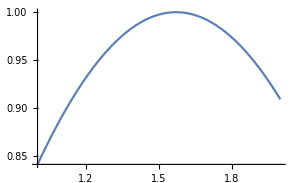
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information